```mathematica
legends={Graphics[{Opacity[0.5],Green,Rectangle[{0,0},{4,1}],Red,Thickness[.03],Dashed,Line[{{0,0.5},{4,.5}}]},ImageSize->100],
Graphics[{Opacity[0.5],Blue,Rectangle[{0,0},{4,1}],Cyan,Thickness[.03],Dashed,Line[{{0,0.5},{4,.5}}]},ImageSize->100],Graphics[{Opacity[0.5],Red,Rectangle[{0,0},{4,1}],Green,Thickness[.03],Dashed,Line[{{0,0.5},{4,.5}}]},ImageSize->100]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
SwatchLegend[{Green,Blue,Red},{"Green","Blue","Red"},LegendMarkerSize->{{50,20}},LegendMarkers->legends]
```

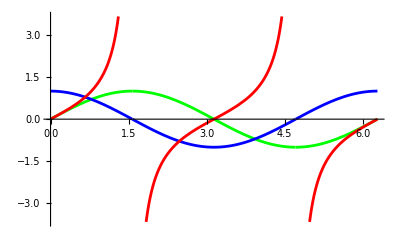

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,0,2π},PlotStyle->{Green,Blue,Red},PlotLegends->SwatchLegend[{Green,Blue,Red},{"Green","Blue","Red"},LegendMarkerSize->{{50,20}},LegendMarkers->legends]]
```